```mathematica
ClearAll["Global`*"]
(*~ MacOS ~*)
main="/Users/mikhailgaerlan/Box Sync/Education/MSU/2015-2016 Fall/PH 4433 Computational Physics/Homework/Homework 9/ohg6-hw9/";
(*~ Windows ~*)
(*main="/Users/Mikhail/Box Sync/Education/MSU/2015-2016 Fall/PH 4433 Computational Physics/Homework/Homework 4/ohg6-hw4/";*)

SetDirectory[main];
$Line=0;
```

```mathematica
rawdata=Table[Import["laplace"<>IntegerString[i,10,1]<>".txt","Data"],{i,1,3}];
data=Table[Table[ImportString[rawdata[[j,i]],"Table"][[1]],{i,Length[rawdata[[j]]]}],{j,1,3}];
```

```mathematica
vectorfield=-Table[Table[Table[{(data[[k,i,j+1]]-data[[k,i,j-1]])/2,(data[[k,i+1,j]]-data[[k,i-1,j]])/2},{i,2,Length[data[[1]]]-1}],{j,2,Length[data[[1]]]-1}],{k,1,3}];
```

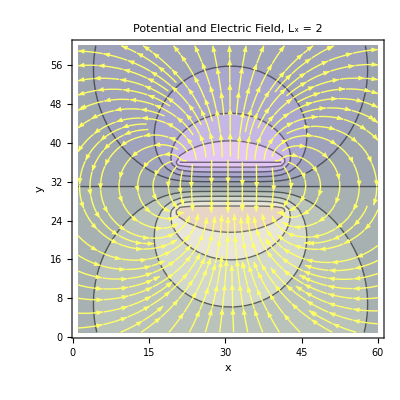

potential1.png

```mathematica
Show[ListContourPlot[data[[1,221;;280,221;;280]],ColorFunction->"PearlColors"],ListStreamPlot[vectorfield[[1,220;;279,220;;279]],StreamStyle->ColorData["Crayola"]["UnmellowYellow"]],BaseStyle->{FontFamily->"Times",FontSize->14},PlotLabel->"Potential and Electric Field, L_x = 2",FrameLabel->{"x","y"}]
Export["potential1.png",%]
```

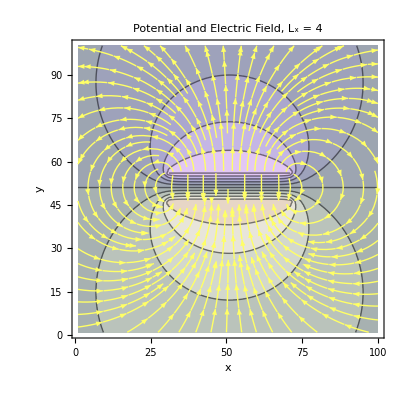

potential2.png

```mathematica
Show[ListContourPlot[data[[2,201;;300,201;;300]],ColorFunction->"PearlColors"],ListStreamPlot[vectorfield[[2,200;;299,200;;299]],StreamStyle->ColorData["Crayola"]["UnmellowYellow"]],BaseStyle->{FontFamily->"Times",FontSize->14},PlotLabel->"Potential and Electric Field, L_x = 4",FrameLabel->{"x","y"}]
Export["potential2.png",%]
```

```mathematica
Show[ListContourPlot[data[[3,51;;450,51;;450]],ColorFunction->"PearlColors"],ListStreamPlot[vectorfield[[3,50;;449,50;;449]],StreamStyle->ColorData["Crayola"]["UnmellowYellow"]],BaseStyle->{FontFamily->"Times",FontSize->14},PlotLabel->"Potential and Electric Field, L_x = 20",FrameLabel->{"x","y"}]
Export["potential3.png",%]
```

-Graphics-

potential3.png

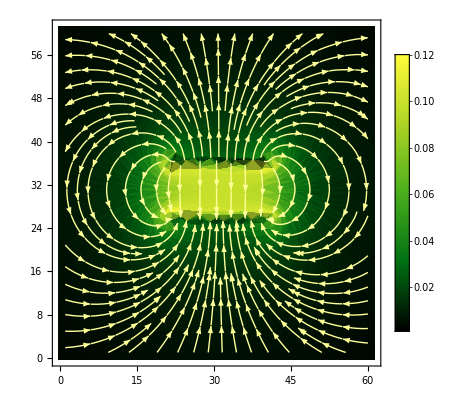

```mathematica
ListStreamDensityPlot[vectorfield[[1,220;;279,220;;279]],ColorFunction->"AvocadoColors",StreamStyle->ColorData["Crayola"]["Canary"],PlotLegends->Automatic]
```

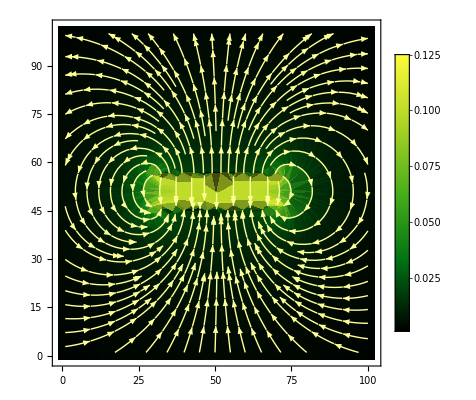

```mathematica
ListStreamDensityPlot[vectorfield[[2,200;;299,200;;299]],ColorFunction->"AvocadoColors",StreamStyle->ColorData["Crayola"]["Canary"],PlotLegends->Automatic]
```

```mathematica
1/{1,0.5,0.1}
```

{1,2.,10.}

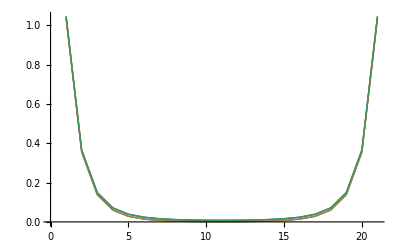

```mathematica
n=1;
ListLinePlot[{chargedensitytoptop[[n]],chargedensitytopbot[[n]],-chargedensitybottop[[n]],-chargedensitybotbot[[n]]},PlotRange->All,PlotTheme->"Classic"]
```

```mathematica
chargedensitytoptop=-Table[Table[(data[[k,256+1,j]]-data[[k,256,j]])/(1/5),{j,251-Interpolation[{2,4,20},InterpolationOrder->2][k]*5,251+Interpolation[{2,4,20},InterpolationOrder->2][k]*5}],{k,1,3}];
chargedensitytopbot=-Table[Table[(data[[k,256,j]]-data[[k,256-1,j]])/(1/5),{j,251-Interpolation[{2,4,20},InterpolationOrder->2][k]*5,251+Interpolation[{2,4,20},InterpolationOrder->2][k]*5}],{k,1,3}];
chargedensitybottop=-Table[Table[(data[[k,246+1,j]]-data[[k,246,j]])/(1/5),{j,251-Interpolation[{2,4,20},InterpolationOrder->2][k]*5,251+Interpolation[{2,4,20},InterpolationOrder->2][k]*5}],{k,1,3}];
chargedensitybotbot=-Table[Table[(data[[k,246,j]]-data[[k,246-1,j]])/(1/5),{j,251-Interpolation[{2,4,20},InterpolationOrder->2][k]*5,251+Interpolation[{2,4,20},InterpolationOrder->2][k]*5}],{k,1,3}];
```

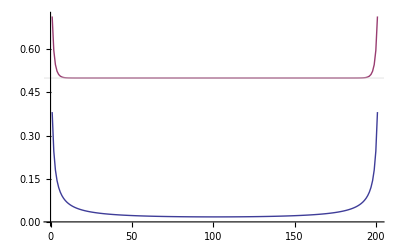

```mathematica
n=3;
ListLinePlot[{chargedensitytoptop[[n]],-chargedensitytopbot[[n]](*,chargedensitybottop[[n]],chargedensitybotbot[[n]]*)},PlotRange->All,PlotTheme->"Classic",GridLines->{None,{0.5}}]
```

```mathematica
Table[Total[Table[(1/10)*(chargedensitytopbot[[j,i]]+chargedensitytopbot[[j,i+1]]),{i,1,Length[chargedensity[[j]]]-1}]],{j,1,3}]
```

{-2.12458,-4.12212,-20.1198}

```mathematica
Flatten[Import["toplower1.txt","Data"]]
```

{-0.599836,-0.548302,-0.524515,-0.512809,-0.506815,-0.503675,-0.502019,-0.501158,-0.500749,-0.500628,-0.500749,-0.501158,-0.502019,-0.503675,-0.506815,-0.512809,-0.524515,-0.548302,-0.599836,-0.722527,-0.313972}

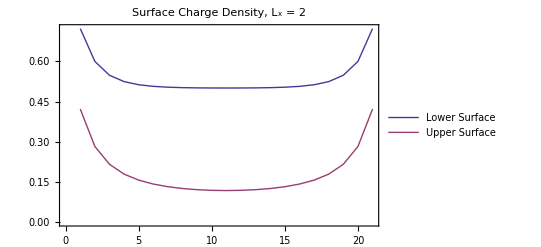

density1.png

```mathematica
ListLinePlot[Abs[{Flatten[Import["toplower1.txt","Data"]],Flatten[Import["topupper1.txt","Data"]]}],PlotTheme->"Classic",PlotLegends->{"Lower Surface","Upper Surface"},BaseStyle->{FontFamily->"Times",FontSize->12},Frame->True,FrameTicks->{{True,False},{True,False}},PlotLabel->"Surface Charge Density, L_x = 2"]
Export["density1.png",%]
```

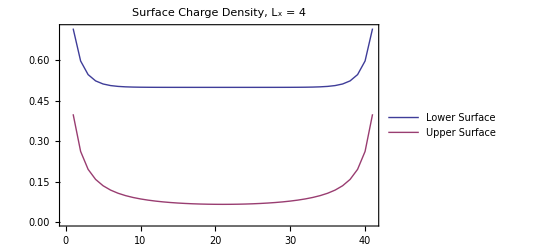

density2.png

```mathematica
ListLinePlot[Abs[{Flatten[Import["toplower2.txt","Data"]],Flatten[Import["topupper2.txt","Data"]]}],PlotTheme->"Classic",PlotLegends->{"Lower Surface","Upper Surface"},BaseStyle->{FontFamily->"Times",FontSize->12},Frame->True,FrameTicks->{{True,False},{True,False}},PlotLabel->"Surface Charge Density, L_x = 4"]
Export["density2.png",%]
```

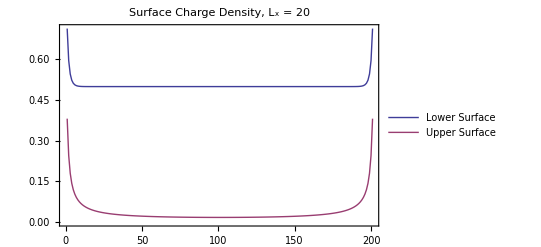

density3.png

```mathematica
ListLinePlot[Abs[{Flatten[Import["toplower3.txt","Data"]],Flatten[Import["topupper3.txt","Data"]]}],PlotTheme->"Classic",PlotLegends->{"Lower Surface","Upper Surface"},BaseStyle->{FontFamily->"Times",FontSize->12},Frame->True,FrameTicks->{{True,False},{True,False}},PlotLabel->"Surface Charge Density, L_x = 20"]
Export["density3.png",%]
```